Ricci scalar R(x,y) = 2   (expected: 2)

Gaussian curvature K(x,y) = 1   (expected: 1)

ℒ_{V_X} g entries = {{0,0},{0,0}}

ℒ_{V_Y} g entries = {{0,0},{0,0}}

ℒ_{V_Z} g entries = {{0,0},{0,0}}

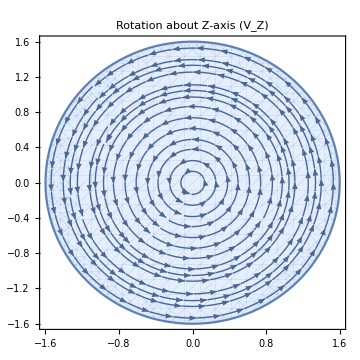
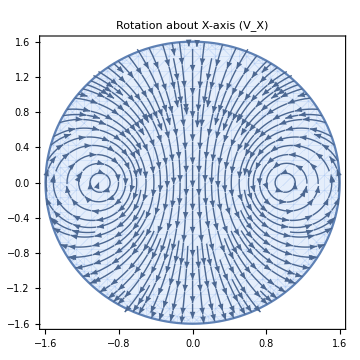
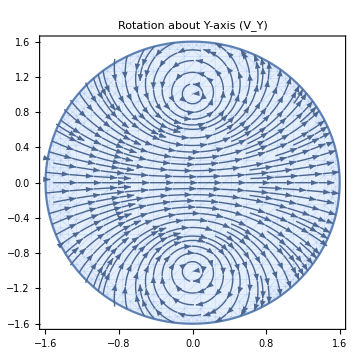

```mathematica
(* =========================================SU(2)/U(1)≃S^2—Fubini–Study metric (K=1),SO(3) Killing fields,verification,and flows.
=========================================*)(*----------Coordinates and stereographic map----------*)ClearAll[x,y,r2,Xs,Ys,Zs,sphMap,Jxy];
r2[x_,y_]:=x^2+y^2;

(*Stereographic from south pole to plane (x,y)*)
Xs[x_,y_]:=2 x/(1+r2[x,y]);
Ys[x_,y_]:=2 y/(1+r2[x,y]);
Zs[x_,y_]:=(1-r2[x,y])/(1+r2[x,y]);

sphMap[x_,y_]:={Xs[x,y],Ys[x,y],Zs[x,y]};              (*R^2->S^2⊂R^3*)
Jxy[x_,y_]:=D[sphMap[ξ,η],{{ξ,η}}]/. {ξ->x,η->y};  (*3×2 Jacobian*)

(*----------Fubini–Study metric in (x,y)----------*)
ClearAll[gFS,gInvFS,detgFS];
gFS[x_,y_]:=(4/(1+r2[x,y])^2) IdentityMatrix[2];  (*ds^2=4(dx^2+dy^2)/(1+r^2)^2*)
gInvFS[x_,y_]:=(1/4) (1+r2[x,y])^2 IdentityMatrix[2];
detgFS[x_,y_]:=Det[gFS[x,y]];

(*----------Christoffels,Ricci,Gaussian curvature----------*)
ClearAll[GammaChr,RicciFS,RscalarFS];
Module[{coords={x,y},gij,gijInv,Γ},gij=gFS[x,y];gijInv=gInvFS[x,y];
(*Γ^k_{ij}=1/2 g^{kl} (∂_i g_{jl}+∂_j g_{il}-∂_l g_{ij})*)Γ=Table[1/2 Sum[gijInv[[k,l]] (D[gij[[j,l]],coords[[i]]]+D[gij[[i,l]],coords[[j]]]-D[gij[[i,j]],coords[[l]]]),{l,2}],{k,2},{i,2},{j,2}];
GammaChr[i_,j_,k_]:=Γ[[k,i,j]];
(*Ricci_ij*)RicciFS[i_,j_]:=Simplify[Sum[D[Γ[[k,i,j]],coords[[k]]],{k,2}]-D[Sum[Γ[[k,i,k]],{k,2}],coords[[j]]]+Sum[Γ[[k,i,j]] Γ[[l,k,l]],{k,2},{l,2}]-Sum[Γ[[k,i,l]] Γ[[l,j,k]],{k,2},{l,2}]];
RscalarFS[]:=Simplify[Sum[gInvFS[x,y][[i,j]] RicciFS[i,j],{i,2},{j,2}]];];

Rval=Simplify[RscalarFS[]];
Kval=Simplify[Rval/2];  (*In 2D:R=2K*)
Print["Ricci scalar R(x,y) = ",Rval,"   (expected: 2)"];
Print["Gaussian curvature K(x,y) = ",Kval,"   (expected: 1)"];

(*----------Ambient rotations and induced Killing fields----------*)
(*Infinitesimal rotations in ℝ^3 about X,Y,Z*)
ClearAll[deltaX,deltaY,deltaZ];
deltaX[X_,Y_,Z_]:={0,-Z,Y};
deltaY[X_,Y_,Z_]:={Z,0,-X};
deltaZ[X_,Y_,Z_]:={-Y,X,0};

(*Pushforward to (x,y):v=(J^T J)^(-1) J^T δ*)
ClearAll[pseudoInv2,pushForward2D,VX,VY,WX,WY,ZX,ZY];
pseudoInv2[J_]:=Simplify[Inverse[Transpose[J].J].Transpose[J]];  (*2×3*)
pushForward2D[δ_]:=Module[{J=Jxy[x,y],d=δ@@sphMap[x,y]},Simplify[pseudoInv2[J].d]    (*returns {Vx(x,y),Vy(x,y)}*)];

{VX[x_,y_],VY[x_,y_]}=pushForward2D[deltaX];  (*about X-axis*)
{WX[x_,y_],WY[x_,y_]}=pushForward2D[deltaY];  (*about Y-axis*)
{ZX[x_,y_],ZY[x_,y_]}=pushForward2D[deltaZ];  (*about Z-axis*)

(*----------Verify Killing:Lie derivative ℒ_V g=0----------*)
ClearAll[LieDerivMetric2D];
LieDerivMetric2D[{Vx_,Vy_}]:=Module[{coords={x,y},gij=gFS[x,y]},Simplify@Table[Sum[{Vx,Vy}[[k]] D[gij[[i,j]],coords[[k]]],{k,2}]+Sum[gij[[i,k]] D[{Vx,Vy}[[k]],coords[[j]]],{k,2}]+Sum[gij[[j,k]] D[{Vx,Vy}[[k]],coords[[i]]],{k,2}],{i,2},{j,2}]];

LVX=LieDerivMetric2D[{VX[x,y],VY[x,y]}]//Simplify;
LVY=LieDerivMetric2D[{WX[x,y],WY[x,y]}]//Simplify;
LVZ=LieDerivMetric2D[{ZX[x,y],ZY[x,y]}]//Simplify;
Print["ℒ_{V_X} g entries = ",LVX];
Print["ℒ_{V_Y} g entries = ",LVY];
Print["ℒ_{V_Z} g entries = ",LVZ];
(*Expect all three to be 2×2 zero matrices*)

regR=1.6;  (*radius of plotting window in (x,y)*)

spZ=StreamPlot[Evaluate@{ZX[x,y],ZY[x,y]},{x,-regR,regR},{y,-regR,regR},StreamPoints->Fine,StreamColorFunction->None,PlotRange->{{-regR,regR},{-regR,regR}},RegionFunction->Function[{xx,yy,vx,vy},xx^2+yy^2<=regR^2],ImageSize->360,StreamMarkers->Arrowheads[.03],PlotLabel->"Rotation about Z-axis (V_Z)"];

spX=StreamPlot[Evaluate@{VX[x,y],VY[x,y]},{x,-regR,regR},{y,-regR,regR},StreamPoints->Fine,StreamColorFunction->None,PlotRange->{{-regR,regR},{-regR,regR}},RegionFunction->Function[{xx,yy,vx,vy},xx^2+yy^2<=regR^2],ImageSize->360,StreamMarkers->Arrowheads[.03],PlotLabel->"Rotation about X-axis (V_X)"];

spY=StreamPlot[Evaluate@{WX[x,y],WY[x,y]},{x,-regR,regR},{y,-regR,regR},StreamPoints->Fine,StreamColorFunction->None,PlotRange->{{-regR,regR},{-regR,regR}},RegionFunction->Function[{xx,yy,vx,vy},xx^2+yy^2<=regR^2],ImageSize->360,StreamMarkers->Arrowheads[.03],PlotLabel->"Rotation about Y-axis (V_Y)"];

Row[{spZ,Spacer[12],spX,Spacer[12],spY}]
```